# disLocate: Sample Analysis

This Notebook, assumes that it is placed in the Examples folder, downloaded in full from the disLocate GitHub.

## Loading in disLocate

### Load the package into this notebook if you have previously installed the disLocate paclet (see InstallPacletExample.nb)

```mathematica
Needs["disLocate`"]
```

### If you are using an older version of Mathematica (below 12.1), uncomment (remove starred brackets) and run the following code instead of above:

```mathematica
(*
SetDirectory[NotebookDirectory[]];
<<disLocate.m
*)
```

#### *You can check the package loaded in correctly, by looking at its version via:

```mathematica
disLocateVersion
```

8.2023-06-12.thesis-M.V8

## Analysis

For a list of documentation files, see: "Guide Page: disLocate"paclet:disLocate/guide/disLocate

```mathematica
(*Import Individual Files*)
SetDirectory[NotebookDirectory[]];
xyl200 = Import["xyl200.csv"]; (*This imports a list of 2d points. Open the csv directly to look at its format*)
xyl400 = Import["xyl400.csv"];
```

### Voronoi Tessellations

Documentation: "PlotVoronoiTessellations"paclet:disLocate/ref/PlotVoronoiTessellations

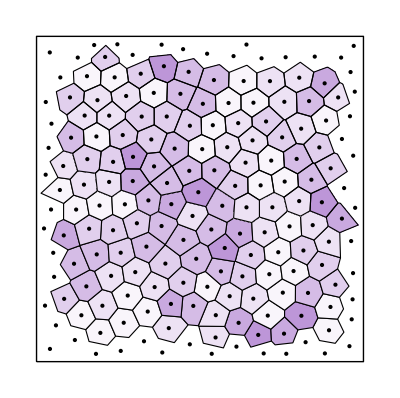
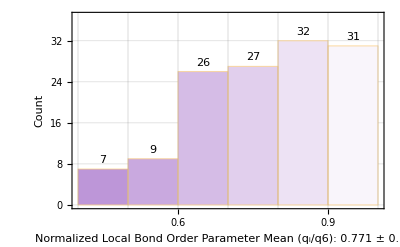

```mathematica
(* Default return of PlotVoronoi Tesselations. Bond Order Parameter used for colouring. This is the type->"bop" option (see below).*)
PlotVoronoiTessellations@xyl200
```

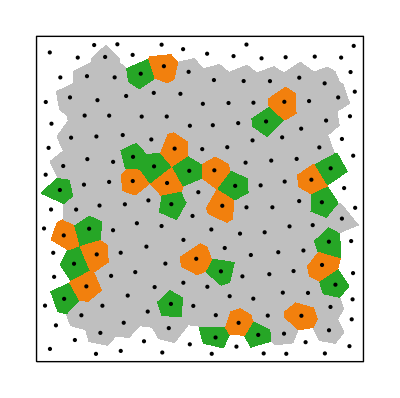
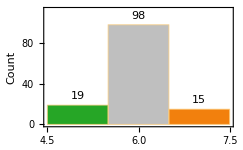

```mathematica
(*Two other colour schemes are available and can be specified using type*)
PlotVoronoiTessellations[xyl200, type->"coord"] (*Voronoi cells coloured by number of sides*)
```

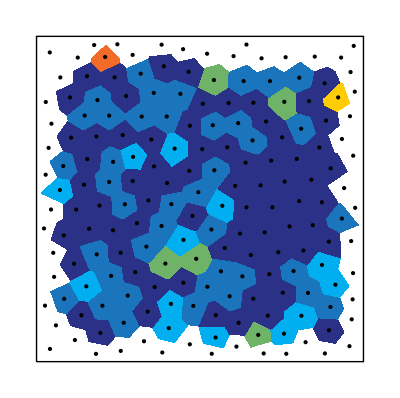
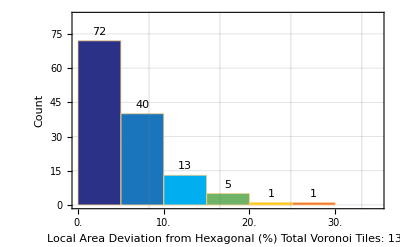

```mathematica
PlotVoronoiTessellations[xyl200, type->"vor"] (*Voronoi cells coloured by area deviation from hexagonal lattice *)
```

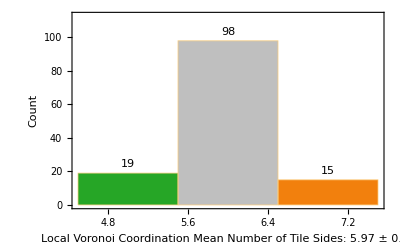
{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
(*You can plot all 3 types of tessellation with one command by using the application operators:*)
PlotVoronoiTessellations[xyl200,scalebar->True, type-> #]&/@{"vor","bop","coord"}
```

```mathematica
(*There is also an option to save all of the output files as a png. You can see the saved output in the folder this notebook is saved in.*)
PlotVoronoiTessellations[xyl200, save->True]
```

{-Graphics-,-Graphics-}

```mathematica
(*If you have a .png of the original AFM image of the particle array, you can overlay the voronoi Tessellation with the image as follows *)
myImage = -Graphics- ;(*Yes. You can just copy paste a png into a cell and save it in a variable. Crazy. I know. *)
(*  Overlay the Nanoparticle Images with the Voronoi Tessellation:  *)
(* a) Image Dimensions tells how many pixels the image is  *)
ImageDimensions[myImage]

(* b) Rescale the points by:  image/box  size  *)
vor=PlotVoronoiTessellations[(410/1000)* xyl200][[1]];

(* c) The double ImageReflect is needed because the jpeg image {0,0} starts at the top left... *)
(*     ...while xy data starts in the bottom left as the origin.  *)
ImageReflect@Show[{ImageReflect[myImage],vor  }]
```

{410,410}

-Graphics-

The PlotVoronoiTessellation function also has options for: 
displaying scalebar, changing image raster, removing points on graphic, changing data truncation type etc. 
For bop type specifically: Changing bin size, setting custom colour gradients etc.
See examples/how to use these options in the documentation file:  "Guide Page: disLocate"paclet:disLocate/guide/disLocate (or find it on our GitHub)
The Documentation also has examples of built in Mathematica functions that could simplify/speed up your disLocate analysis.

### Pair Correlation Function

Documentation: "PlotPairCorrelationFunction"paclet:disLocate/ref/PlotPairCorrelationFunction

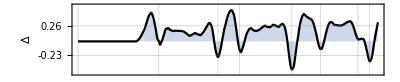
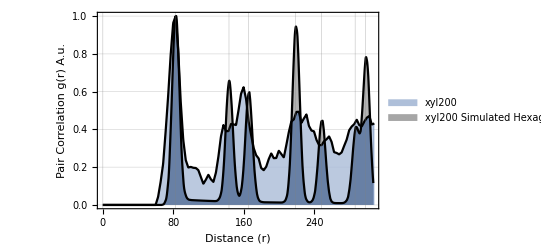
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
xyl200 | 82.6931 | 82.6236 | 2.5267 | 183 | 187

```mathematica
(*Default output of Pair Correlation Function on single dataset:*)
PlotPairCorrelationFunction@xyl200
```

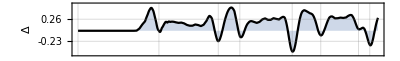
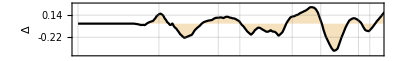
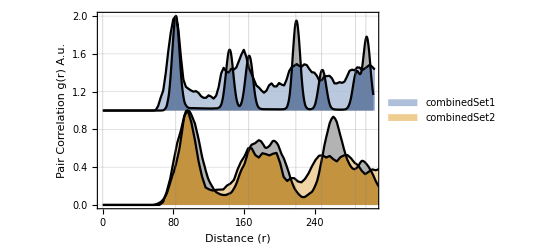
-Graphics-
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
combinedSet1 | 82.6931 | 82.6236 | 2.5267 | 183 | 187
combinedSet2 | 96.3248 | 97.0426 | 7.45882 | 131 | 136

```mathematica
(*It is possible to plot multiple datasets for comparison, by passing a list of datasets *)
(*Place data in array*)
combinedSet = {xyl200,xyl400};
PlotPairCorrelationFunction@combinedSet
```

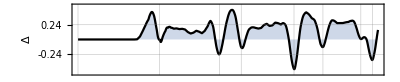
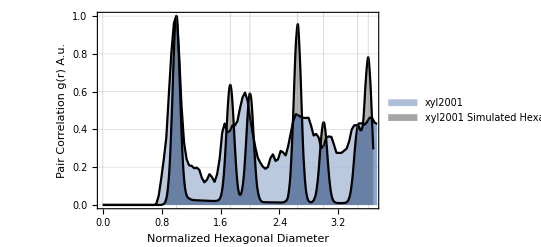
-Graphics-
-Graphics-
 | First Peak
g(r) | Expected Spacing
(Hexatic Lattice) | Expected Disorder
(Hexatic Lattice) | Particles
(data) | Particles
(lattice)
xyl2001 | 82.6931 | 82.6236 | 2.5267 | 183 | 187

```mathematica
(*It is possible to normalize the x-axis to the expected radius of a single particle*)
PlotPairCorrelationFunction[xyl200, normalized->True]
```

The PlotPairCorrelationFunction also has options for:
Unscaling the y axis to be not-normalized, selecting custom colours for each dataset, changing lattice type, changing dataset labels and more. 
Read the documentation here: "PlotPairCorrelationFunction"paclet:disLocate/ref/PlotPairCorrelationFunction for examples.

### AverageNeighbourDistance

Documentation: "AverageFirstNeighbourDistance"paclet:disLocate/ref/AverageFirstNeighbourDistance

```mathematica
(*Computes average distance to nearest particle (or to nearest n particles. See documentation)*)
AverageFirstNeighbourDistance@xyl200
```

71.3071

### ExpectedHexagonalDiameter

Documentation: "ExpectedHexagonalDiameter"paclet:disLocate/ref/ExpectedHexagonalDiameter

```mathematica
(*Computes expected particle radius, assuming hexagonal lattice.*)
ExpectedHexagonalDiameter@xyl200
```

{82.6236,2.5267}

### BondOrderParameter

Documentation: "BondOrderParameter"paclet:disLocate/ref/BondOrderParameter

```mathematica
(*Computes bond order parameters from a set of 2d points of some degree (in this case 6). Normalized by default (see Documentation). *)
BondOrderParameter[xyl200,6]
```

{0.803248,0.426996,0.949183,0.511265,0.94679,0.851557,0.979255,0.54908,0.921791,0.442524,0.96313,0.809117,0.950957,0.69959,0.913181,0.879245,0.565638,0.70271,0.807586,0.901604,0.843682,0.673263,0.908736,0.885982,0.911882,0.677434,0.700968,0.760721,0.846289,0.790447,0.911526,0.863826,0.965426,0.644413,0.704744,0.793937,0.655472,0.612278,0.619846,0.725799,0.775051,0.985359,0.741839,0.444589,0.624308,0.820158,0.620981,0.559878,0.597808,0.715616,0.6764,0.886235,0.702633,0.905806,0.615133,0.893342,0.742893,0.553898,0.872555,0.92117,0.951204,0.834559,0.647457,0.80966,0.954747,0.511349,0.46862,0.860922,0.653323,0.460352,0.914345,0.922591,0.867838,0.715957,0.626056,0.540891,0.892093,0.977846,0.629609,0.651559,0.671857,0.751336,0.87405,0.651433,0.742844,0.860416,0.956799,0.705952,0.69609,0.489597,0.646086,0.96107,0.803922,0.753572,0.821427,0.621254,0.779053,0.77092,0.953682,0.729431,0.848891,0.739728,0.924862,0.857142,0.909587,0.784352,0.772659,0.733263,0.856613,0.894532,0.670503,0.961651,0.928207,0.833959,0.671176,0.834669,0.789095,0.848314,0.871314,0.672407,0.935931,0.558377,0.69497,0.972958,0.834387,0.858489,0.936689,0.917359,0.799134,0.696664,0.484475,0.756041}

### BondOrderParameter

Documentation: "BondOrderParameter"paclet:disLocate/ref/BondOrderParameter

```mathematica
(*Computes bond order parameters from a set of 2d points of some degree (in this case 6). Normalized by default (see Documentation). *)
bops200 =BondOrderParameter[xyl200,6];
Mean@bops200
```

0.770507

### CoordinationNeighbourCloud

Documentation: "CoordinationNeighbourCloud"paclet:disLocate/ref/CoordinationNeighbourCloud

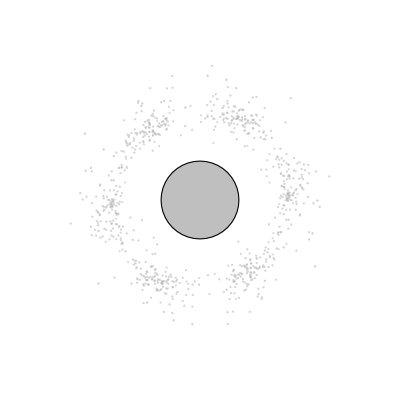
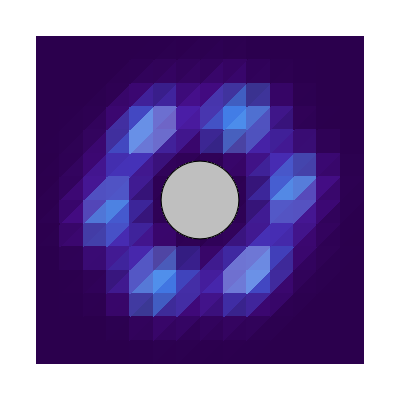
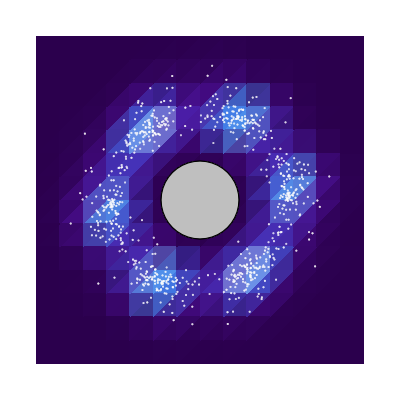

```mathematica
(* Coordination cloud shows the probability of Neighbours relative to each object *) 
(* Similar to the Fourier Transform, except it can be separated by Coordination   *)

CoordinationNeighbourCloud@xyl200
```

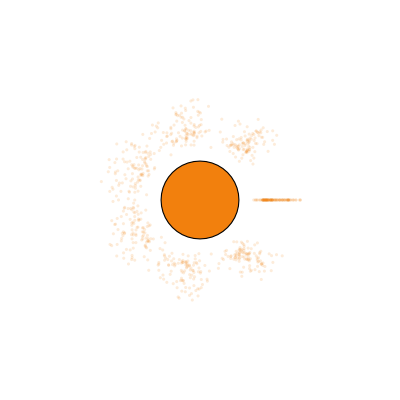
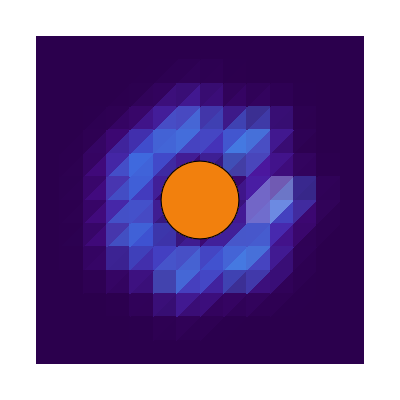
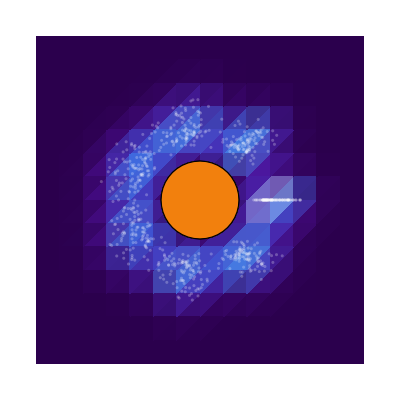

```mathematica
(*   Only select the particles that have 7 neighbours *)

CoordinationNeighbourCloud[xyl200,coord->7]
```